# Print Dielectric Tensor

## Open Additional files:

## Set Parameters by opening a Parameter Window or set them in the next cell down. Get dispersion routines by evaluating Disper_no_package.nb Get plotting and printing routines by evaluating PlotPack.nb Routines return a 6 element list in the order Eps{xx,yy,zz,xy,xz,yz}

## Parameters

### RF Parameters

```mathematica
freq=55500;
c=3. 10^8;
k0=(2 N[π] freq 10^6)/c;
nz  =0.1;
kz= nz * k0;
nx0=0.3;
```

### Plasma Parameters

```mathematica
ne0=.3  10^20;
B=2.0;

etaList=Table[0.,{i,1,5}];
etaList⟦1⟧=1.;etaList⟦2⟧=0.0;etaList⟦3⟧=0.;
etaList⟦4⟧=0.;etaList⟦5⟧=0.;

(* N.B. For Linear slab model Te Xmin and Te Xmax are defined above.  TList here gives the ratio of various Ti to Te (i.e. TList[[1]] = 1.0 always)  *)
TList=Table[0.,{i,1,6}];
TList⟦1⟧=1.;TList⟦2⟧=1.;
TList⟦3⟧=0. ;TList⟦4⟧=0.;
TList⟦5⟧=0.;TList⟦6⟧=0.;

modelList =Table[0,{i,1,6}];
modelList[[1]]=2; modelList[[2]]=1;
modelList[[3]]=0; modelList[[4]]=0;
modelList[[5]]=0; modelList[[6]]=0;

nminList=Table[0.,{i,1,6}];
nminList⟦1⟧=-1;nminList⟦2⟧=-2;
nminList⟦3⟧=-2;nminList⟦4⟧=-2;
nminList⟦5⟧=-2;nminList⟦6⟧=-2;

nmaxList=Table[0.,{i,1,6}];
nmaxList⟦1⟧=1;nmaxList⟦2⟧=2;
nmaxList⟦3⟧=2;nmaxList⟦4⟧=2;
nmaxList⟦5⟧=2;nmaxList⟦6⟧=2;
```

### Plot Parameters

```mathematica
dataSet="DIII-D ECH slab";
xmin=1.9;
xmax=2.1;
nPoints=101;
```

Print Eps for different models

### Print ε for different models

```mathematica
Do[modelList[[i]]=0, {i,1,6}];e0=EpsGeneral[freq,ne0,B,nz,nx0,etaList,TList,nminList,nmaxList,modelList,True];

Do[modelList[[i]]=1, {i,1,6}];e1=EpsGeneral[freq,ne0,B,nz,nx0,etaList,TList,nminList,nmaxList,modelList,True];

Do[modelList[[i]]=2, {i,1,6}];e2=EpsGeneral[freq,ne0,B,nz,nx0,etaList,TList,nminList,nmaxList,modelList,True];

paramPrint[{dataSet,ne0,B,freq,nz,nx0,etaList,TList,modelList}];
```

EpsGeneral    species=1    model for this species =0

Eps[i]={43.3939,43.3939,-0.785395,-43.7849,0,0}

EpsGeneral    species=2    model for this species =0

Eps[i]={-0.000427775,-0.000427775,-0.000427775,-2.35092×10^-7,0,0}

EpsGeneral    species=1    model for this species =1

Eps[i]={55.6999+13.9419 ⅈ,55.6804+13.9371 ⅈ,-0.776503+0.0100047 ⅈ,13.9395-56.0812 ⅈ,-0.329875-0.373507 ⅈ,0.373507-0.329841 ⅈ}

EpsGeneral    species=2    model for this species =1

Eps[i]={-0.000427775,-0.000427775,-0.000427775,0.-2.35092×10^-7 ⅈ,0,0}

EpsGeneral    species=1    model for this species =2

Eps[i]={55.6999+13.9419 ⅈ,55.6804+13.9371 ⅈ,-0.776504+0.0100029 ⅈ,13.9395-56.0811 ⅈ,-0.329819-0.373443 ⅈ,0.373378-0.329727 ⅈ}

EpsGeneral    species=2    model for this species =2

Eps[i]={-0.000415087,-0.000417457,-0.000427342,0.-2.15792×10^-7 ⅈ,0,0.-2.17065×10^-10 ⅈ}

dataSet=DIII-D ECH slab

ne0=3.×10^19

B=2.

freq=55500

nz=0.1

nx0=0.3

etaList={1.,0.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={2,2,2,2,2,2}

```mathematica
WarmEpsMaxwell[freq,ne0,B,nz,nx0,etaList,TList,nminList,nmaxList,True]
```

Eps full Bessel function, summed over harmonic    species=0

Eps[i]={55.6999+13.9419 ⅈ,55.6804+13.9371 ⅈ,-0.776504+0.0100029 ⅈ,13.9395-56.0811 ⅈ,-0.329819-0.373443 ⅈ,0.373378-0.329526 ⅈ}

Eps full Bessel function, summed over harmonic    species=1

Eps[i]={-0.000415087,-0.000417457,-0.000427342,0.-2.15792×10^-7 ⅈ,0,0.-0.0204068 ⅈ}

{56.6995+13.9419 ⅈ,56.68+13.9371 ⅈ,0.223068+0.0100029 ⅈ,13.9395-56.0811 ⅈ,-0.329819-0.373443 ⅈ,0.373378-0.349933 ⅈ}

### Print/Plot Hermitian and anti - Hermitian parts

```mathematica
Clear[epsH]
```

```mathematica
epsH[b_]:=Module[{eps},B0=b;
eps=EpsGeneral[freq,ne0,B0,nz,nx0,etaList,TList,nminList,nmaxList,modelList];
{Re[eps[[1]]],Re[eps[[2]]],Re[eps[[3]]],I*Im[eps[[4]]],Re[eps[[5]]],I*Im[eps[[6]]]}];
epsA[b_]:=Module[{eps},B0=b;
eps=EpsGeneral[freq,ne0,B0,nz,nx0,etaList,TList,nminList,nmaxList,modelList];
{I*Im[eps[[1]]],I*Im[eps[[2]]],I*Im[eps[[3]]],Re[eps[[4]]],I*Im[eps[[5]]],Re[eps[[6]]]}]
```

```mathematica
epsH[2.]
epsA[2.]
```

{56.6995,56.68,0.223068,0.-56.0811 ⅈ,-0.329819,0.-0.329727 ⅈ}

{0.+13.9419 ⅈ,0.+13.9371 ⅈ,0.+0.0100029 ⅈ,13.9395,0.-0.373443 ⅈ,0.373378}

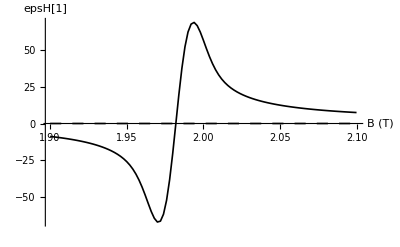

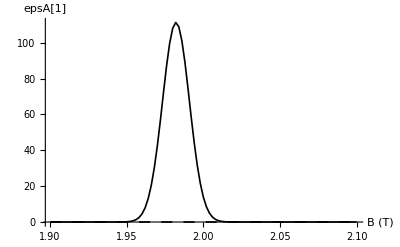

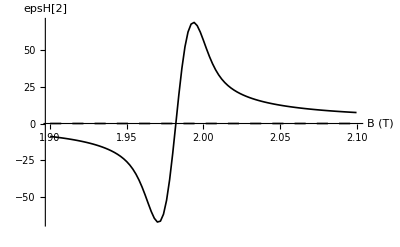

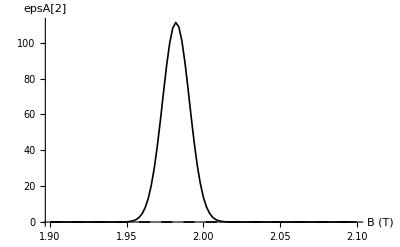

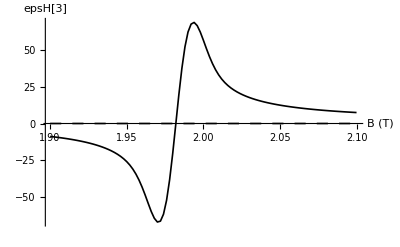

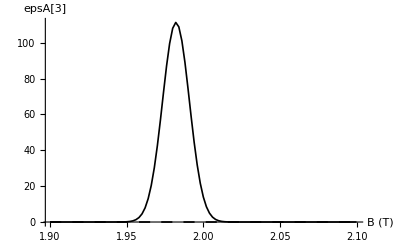

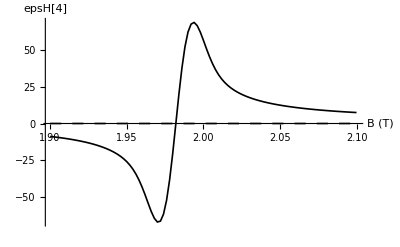

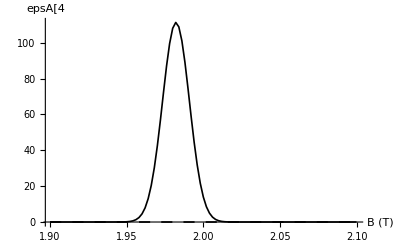

```mathematica
h1=Table[{b,epsH[b][[1]]},{b,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexVectorListPlot[h1,"B (T)","epsH[1]"]
a1=Table[{b,Im[epsA[b][[1]]]},{b,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexVectorListPlot[a1,"B (T)","epsA[1]",PlotRange->All]
h2=Table[{b,epsH[b][[2]]},{b,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexVectorListPlot[h1,"B (T)","epsH[2]"]
a2=Table[{b,Im[epsA[b][[2]]]},{b,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexVectorListPlot[a1,"B (T)","epsA[2]",PlotRange->All]
h3=Table[{b,epsH[b][[3]]},{b,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexVectorListPlot[h1,"B (T)","epsH[3]"]
a3=Table[{b,Im[epsA[b][[3]]]},{b,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexVectorListPlot[a1,"B (T)","epsA[3]",PlotRange->All]
h4=Table[{b,epsH[b][[4]]},{b,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexVectorListPlot[h1,"B (T)","epsH[4]"]
a4=Table[{b,Im[epsA[b][[4]]]},{b,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexVectorListPlot[a1,"B (T)","epsA[4",PlotRange->All]
h5=Table[{b,epsH[b][[5]]},{b,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexVectorListPlot[h1,"B (T)","epsH[5"]
a5=Table[{b,Im[epsA[b][[5]]]},{b,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexVectorListPlot[a5,"B (T)","epsA[5]",PlotRange->All]
h6=Table[{b,epsH[b][[6]]},{b,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexVectorListPlot[h6,"B (T)","epsH[6]"]
a6=Table[{b,Im[epsA[b][[6]]]},{b,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexVectorListPlot[a6,"B (T)","epsA[6]",PlotRange->All]
```

### Print Gamma for each species

```mathematica
Warmgamma[freq,B,nx0,TList]
```

{0.000172656,0.316997,0.,0.,0.,0.}

### Break down by species and harmonic

```mathematica
SigMaxOneHarmonicOneSpecies[freq_,ne_,B_,nz_,nx_,etaList_List,TList_List,nharm_,nspec_,print_:False]:=Module[{n0,B0,eta,mass,chg,T,fp,fc,v,sig},n0=ne/10^6;B0=B 10^4;eta[0]=1.;Do[eta[i]=etaList⟦i⟧,{i,1,5}];Do[T[i]=TList⟦i+1⟧,{i,0,5}];
Print[{T[1],T[2]}];
Print[TList];
Print[{eta[0],eta[1]}];
nHarmonic =nharm;
i=nspec;
Print["i = ",i];
mass[0]=1.;mass[1]=1836.;mass[2]=3670.;mass[3]=5497.;mass[4]=5496.;mass[5]=7294.;chg[0]=-1.;chg[1]=1.;chg[2]=1.;chg[3]=1.;chg[4]=2.;chg[5]=2.;fp=N[(8.98 √((n0 eta[i] chg[i]^2)/mass[i]))/10^3];fc=N[(2.80 B0 chg[i])/mass[i]];v=N[√(T[i]/(mass[i] 256))];
Print["v = ", v];
sig=SigmaMaxn[fp,fc,freq,v,nz,nx,nHarmonic];If[print==True,
(If[fp v>0,
(Print["\n\nEps full Bessel function,  harmonic = ",nHarmonic,", species = ",i];Print["Eps[i]=",Chop[sig]])]),];sig]
```

```mathematica
SigMaxOneHarmonicOneSpecies[freq,ne0,B,nz,nx0,etaList,TList,1,1,True];
```

Eps full Bessel function  harmonic = 1 species = 1

Eps[i]={-0.000157833,-0.0000869848,-0.0000500326,0.-0.000111749 ⅈ,-0.861109,0.+0.609682 ⅈ}

```mathematica
ispec=1;Do[SigMaxOneHarmonicOneSpecies[freq,ne0,B,nz,nx0,etaList,TList,iharm,ispec,True],{iharm,nminList[[ispec]],nmaxList[[ispec]]}]
```

Eps full Bessel function,  harmonic = -1, species = 1

Eps[i]={-0.00015766,-0.0000868893,-0.0000499776,0.+0.000111626 ⅈ,0.861109,0.+0.609682 ⅈ}

Eps full Bessel function,  harmonic = 0, species = 1

Eps[i]={0,-0.000170819,-0.000319439,0,0,0.-1.47079 ⅈ}

Eps full Bessel function,  harmonic = 1, species = 1

Eps[i]={-0.000157833,-0.0000869848,-0.0000500326,0.-0.000111749 ⅈ,-0.861109,0.+0.609682 ⅈ}

```mathematica
ispec=2;Do[SigMaxOneHarmonicOneSpecies[freq,ne0,B,nz,nx0,etaList,TList,iharm,ispec,True],{iharm,nminList[[ispec]],nmaxList[[ispec]]}]
```

{1.,0.}

{1.,1.,0.,0.,0.,0.}

{1.,1.}

i = 2

v = 0.

{1.,0.}

{1.,1.,0.,0.,0.,0.}

{1.,1.}

i = 2

v = 0.

{1.,0.}

{1.,1.,0.,0.,0.,0.}

{1.,1.}

i = 2

v = 0.

{1.,0.}

{1.,1.,0.,0.,0.,0.}

{1.,1.}

i = 2

v = 0.

{1.,0.}

{1.,1.,0.,0.,0.,0.}

{1.,1.}

i = 2

v = 0.

{1.,1.,0.,0.,0.,0.}

1..1.

i = 2

v = 0.

{1.,0.}

{1.,1.,0.,0.,0.,0.}

1..1.

i = 2

v = 0.

{1.,0.}

{1.,1.,0.,0.,0.,0.}

1..1.

i = 2

v = 0.

{1.,0.}

{1.,1.,0.,0.,0.,0.}

1..1.

i = 2

v = 0.

{1.,0.}

{1.,1.,0.,0.,0.,0.}

1..1.

i = 2

v = 0.

```mathematica
WarmEpsMaxwell[freq,ne0,B,nz,nx0,etaList,TList,nminList,nmaxList,True]
```

Eps full Bessel function, harmonic = -1    species = 0

Eps[i]={55.8953+13.9419 ⅈ,55.876+13.9371 ⅈ,0.00883458+0.0100029 ⅈ,13.9395-55.8857 ⅈ,-1.4972-0.373443 ⅈ,0.373378-1.49694 ⅈ}

Eps full Bessel function, harmonic = 0    species = 0

Eps[i]={0,-0.000271142,-0.785305,0,0,0.+2.33459 ⅈ}

Eps full Bessel function, harmonic = 1    species = 0

Eps[i]={-0.195435,-0.195368,-0.0000337435,0.-0.195402 ⅈ,1.16738,0.-1.16718 ⅈ}

Eps full Bessel function, summed over harmonic    species=0

Eps[i]={55.6999+13.9419 ⅈ,55.6804+13.9371 ⅈ,-0.776504+0.0100029 ⅈ,13.9395-56.0811 ⅈ,-0.329819-0.373443 ⅈ,0.373378-0.329526 ⅈ}

Eps full Bessel function, harmonic = -2    species = 1

Eps[i]={-0.0000497423,-0.0000363416,-3.94204×10^-6,0.+0.0000422739 ⅈ,0.135917,0.+0.11551 ⅈ}

Eps full Bessel function, harmonic = -1    species = 1

Eps[i]={-0.00015766,-0.0000868893,-0.0000499776,0.+0.000111626 ⅈ,0.861109,0.+0.609682 ⅈ}

Eps full Bessel function, harmonic = 0    species = 1

Eps[i]={0,-0.000170819,-0.000319439,0,0,0.-1.47079 ⅈ}

Eps full Bessel function, harmonic = 1    species = 1

Eps[i]={-0.000157833,-0.0000869848,-0.0000500326,0.-0.000111749 ⅈ,-0.861109,0.+0.609682 ⅈ}

Eps full Bessel function, harmonic = 2    species = 1

Eps[i]={-0.0000498518,-0.0000364216,-3.95072×10^-6,0.-0.000042367 ⅈ,-0.135917,0.+0.11551 ⅈ}

Eps full Bessel function, summed over harmonic    species=1

Eps[i]={-0.000415087,-0.000417457,-0.000427342,0.-2.15792×10^-7 ⅈ,0,0.-0.0204068 ⅈ}

{56.6995+13.9419 ⅈ,56.68+13.9371 ⅈ,0.223068+0.0100029 ⅈ,13.9395-56.0811 ⅈ,-0.329819-0.373443 ⅈ,0.373378-0.349933 ⅈ}